```mathematica
p/(2Pi)*Integrate[(a+b*Cos[k]+c*Cos[k]^2)/(x+y*Cos[k]+z*Cos[k]^2),k]
```

(p (c k+(√2 (c (y^2-2 x z+y √(y^2-4 x z))+z (2 a z-b (y+√(y^2-4 x z)))) ArcTanh[((y-2 z+√(y^2-4 x z)) Tan[k/2])/(√(-2 y^2+4 z (x+z)-2 y √(y^2-4 x z)))])/(√(y^2-4 x z) √(-y^2+2 z (x+z)-y √(y^2-4 x z)))-(√2 (c (-y^2+2 x z+y √(y^2-4 x z))+z (-2 a z+b (y-√(y^2-4 x z)))) ArcTanh[((-y+2 z+√(y^2-4 x z)) Tan[k/2])/(√(-2 y^2+4 z (x+z)+2 y √(y^2-4 x z)))])/(√(y^2-4 x z) √(-y^2+2 z (x+z)+y √(y^2-4 x z)))))/(2 π z)

```mathematica
NIntegrate[p/(2Pi)(a+b*Cos[k]+c*Cos[k]^2)/(x+y*Cos[k]+z*Cos[k]^2),{k,-Pi,Pi}]/.{a->Jtwo,b->Jone,c->2Jtwo,x->J^2-2J*Jtwo-z^2,y->2*J*Jone,z->4J*Jtwo}
```

NIntegrate[(p (Jtwo+Jone Cos[k]+(2 Jtwo) Cos[k]^2))/((2 π) ((J^2-2 J Jtwo-z^2)+(2 J Jone) Cos[k]+(4 J Jtwo) Cos[k]^2)),{k,-π,π}]

```mathematica
G11[J_,Jone_,Jtwo_,p_,zR_Real]:=NIntegrate[(p ((-J+Jtwo-zR)-Jone Cos[k]-(2 Jtwo) Cos[k]^2))/((2 π) ((J^2-2 J Jtwo-zR^2)+(2 J Jone) Cos[k]+(4 J Jtwo) Cos[k]^2)),{k,-π,π}]
```

```mathematica
G22[J_,Jone_,Jtwo_,p_,zR_Real]:=NIntegrate[(p ((-J+Jtwo+zR)-Jone Cos[k]-(2 Jtwo) Cos[k]^2))/((2 π) ((J^2-2 J Jtwo-zR^2)+(2 J Jone) Cos[k]+(4 J Jtwo) Cos[k]^2)),{k,-π,π}]
```

```mathematica
G12[J_,Jone_,Jtwo_,p_,zR_Real]:=NIntegrate[(p (Jtwo+Jone Cos[k]+(2 Jtwo) Cos[k]^2))/((2 π) ((J^2-2 J Jtwo-zR^2)+(2 J Jone) Cos[k]+(4 J Jtwo) Cos[k]^2)),{k,-π,π}]
```

```mathematica
Nulls[Jtwo_,z_]:=1-G11[1,0.1,Jtwo,0.1,z]-G22[1,0.1,Jtwo,0.1,z]-G12[1,0.1,Jtwo,0.1,z]^2+G11[1,0.1,Jtwo,0.1,z]G22[1,0.1,Jtwo,0.1,z]
```

```mathematica
Lister[Plusminus_,Xstart_,StartIteration_,Jone_,p_] := Module[{lst={{Xstart,FindRoot[Nulls[Xstart,z],{z,StartIteration}]}}},
Do[
Jtwoo=Plusminus(n+1)*0.0005;
a=FindRoot[Nulls[Jtwoo,z]==0,{z,z/.lst[[n,2]]}]
;
AppendTo[lst,{Jtwoo,a}];
,{n,1,199,1}
];
lst
]
```

```mathematica
moduler[list_] := Module[{lst := {}},
Do [
AppendTo [lst,{list[[n,1]],z/.list[[n,2]]}];
,{n,1,200,1}
];
lst
]
```

```mathematica
Fueger[lst1_,lst2_] := Module[{lst={}},
Do[
AppendTo[lst,lst1[[n]]]
,{n,1,200,1}];
Do[
AppendTo[lst,lst2[[n]]]
,{n,1,200,1}];
lst
]
```

```mathematica
√(J^4/(J^2+J a)+(J^3 a)/(J^2+J a)+(J^2 a^2)/(2 (J^2+J a))+(J a^3)/(8 (J^2+J a))-1/(8 (J^2+J a))(√(256 J^4 J q^2+512 J^3 J q^2 a+64 J^6 a^2+320 J^2 J q^2 a^2+96 J^5 a^3+64 J  J q^2 a^3+52 J^4 a^4+12 J^3 a^5+J^2 a^6)))/.{J->1,q->0.1,a->2*-0.1}
```

0.8545

```mathematica
√(J^4/(J^2+J a)+(J^3 a)/(J^2+J a)+(J^2 a^2)/(2 (J^2+J a))+(J a^3)/(8 (J^2+J a))+1/(8 (J^2+J a))(√(256 J^4 J q^2+512 J^3 J q^2 a+64 J^6 a^2+320 J^2 J q^2 a^2+96 J^5 a^3+64 J  J q^2 a^3+52 J^4 a^4+12 J^3 a^5+J^2 a^6)))/.{J->1,q->0.1,a->2*0.1}
```

1.13828

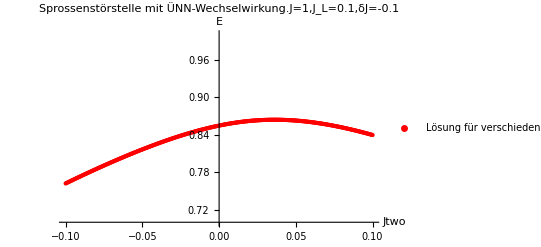

```mathematica
P = ListPlot[Fueger[moduler[Lister[-1,-0.0005,0.8545000070855778,0.1,-0.1]],moduler[Lister[1,0.0005,0.8545000070855778,0.1,-0.1]]],AxesLabel->{Jtwo,"E"},PlotRange->{0.7,1},PlotLegends->{"Lösung für verschiedene Jtwos"},PlotLabel->"Sprossenstörstelle mit ÜNN-Wechselwirkung.J=1,J_L=0.1,δJ=-0.1",PlotStyle->{Red,PointSize[Small]}]
```

```mathematica
Inv[Jone_,Jtwo_] := Piecewise[{{ArcCos[-Jone/(4*Jtwo)],-Jone>4*Jtwo},{0,-Jone<4*Jtwo}}]
```

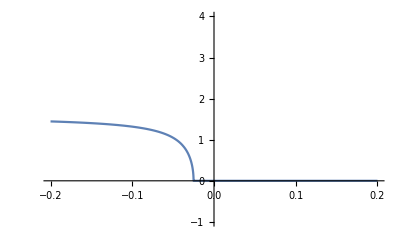

```mathematica
Plot[Inv[0.1,Jtwo],{Jtwo,-0.2,0.2},PlotRange->{-1,4}]
```

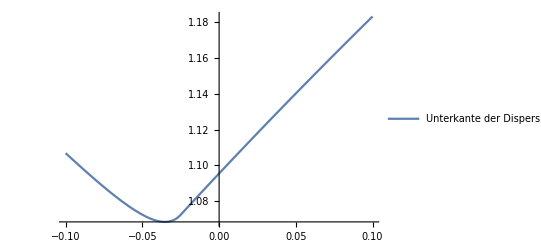

```mathematica
G = Plot[Sqrt[1+2(0.1*Cos[Inv[0.1,Jtwo]]+Jtwo*Cos[2*Inv[0.1,Jtwo]])],{Jtwo,-0.1,0.1},PlotLegends->{"Unterkante der Dispersion"}]
```

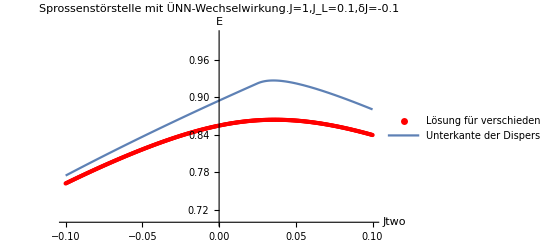

```mathematica
Show[P,G]
```

```mathematica
GLow[J_,Jone_,Jtwo_] := Sqrt[J+2*(Jone*Cos[Inv[Jone,Jtwo]]+Jtwo*Cos[2*Inv[Jone,Jtwo]])]
```

```mathematica
differ[PlusMinus_,Jone_,list_] := Module[{lst = {}},
Do[
Jtwoo = PlusMinus*n*0.0005;
AppendTo[lst,{Jtwoo,-GLow[1,Jone,Jtwoo]+list[[n,2]]}];
,{n,1,200,1}
];
lst
]
```

```mathematica
differ[-1,0.1,{{-0.005,0.8518170212146641},{-0.01,0.8488372997456294},{-0.015,0.8455788532760256},{-0.02,0.8420600465393536},{-0.025,0.8382990565930841},{-0.03,0.8343134421054639},{-0.035,0.8301198271341518},{-0.04,0.8257336909812681},{-0.045,0.8211692487208532},{-0.05,0.816439404137469},{-0.055,0.8115557569346296},{-0.06,0.8065286479886997},{-0.065,0.8013672291799866},{-0.07,0.7960795472625412},{-0.075,0.7906726339386496},{-0.08,0.7851525966034867},{-0.085,0.7795247060577173},{-0.09,0.7737934788817714},{-0.095,0.7679627531841818},{-0.1,0.7620357571513292}}]
```

{{-0.005,0.0370024},{-0.01,0.0343388},{-0.015,0.0319176},{-0.02,0.0297197},{-0.025,0.0277263},{-0.03,0.0259191},{-0.035,0.0242805},{-0.04,0.0227944},{-0.045,0.0214457},{-0.05,0.0202206},{-0.055,0.0191066},{-0.06,0.0180925},{-0.065,0.017168},{-0.07,0.0163243},{-0.075,0.0155531},{-0.08,0.0148474},{-0.085,0.0142007},{-0.09,0.0136073},{-0.095,0.0130622},{-0.1,0.0125609}}

```mathematica
differ[1,0.1,{{0.005,0.8545000070855844},{0.01,0.8589093531704773},{0.015,0.8606073725318385},{0.02,0.8619532730957528},{0.025,0.8629404859227445},{0.03,0.8635661785075325},{0.035,0.8638313182322822},{0.04,0.8637405121390841},{0.045,0.8633016514146582},{0.05,0.8625254108557843},{0.055,0.8614246641766539},{0.06,0.8600138750800655},{0.065,0.8583085143122512},{0.07,0.8563245384271406},{0.075,0.8540779508668574},{0.08,0.8515844524689898},{0.085,0.8488591789933743},{0.09,0.8459165167027465},{0.095,0.8427699840064636},{0.1,0.8394321663097011}}]
```

{{0.005,0.0455},{0.01,0.0466292},{0.015,0.050436},{0.02,0.0545619},{0.025,0.255094},{0.03,0.0619967},{0.035,0.06276},{0.04,0.0622724},{0.045,0.06106},{0.05,0.059429},{0.055,0.0575669},{0.06,0.0555916},{0.065,0.0535788},{0.07,0.0515773},{0.075,0.0496182},{0.08,0.0477208},{0.085,0.0458968},{0.09,0.0441521},{0.095,0.0424894},{0.1,0.0409087}}

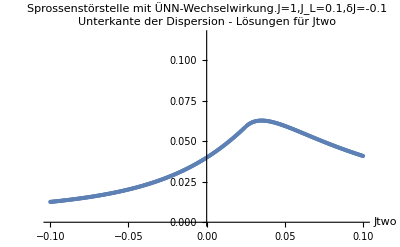

```mathematica
ListPlot[Fueger[differ[-1,0.1,moduler[Lister[-1,-0.0005,0.8545000070855778,0.1,-0.1]]],differ[1,0.1,moduler[Lister[1,0.0005,0.8545000070855778,0.1,-0.1]]]],AxesLabel->{Jtwo,"Unterkante der Dispersion - Lösungen für Jtwo"}, PlotLabel->"Sprossenstörstelle mit ÜNN-Wechselwirkung.J=1,J_L=0.1,δJ=-0.1"]
```

```mathematica
Maxfinder[list_] := Module[{gross=0,spot=0},
Do[
If[list[[n,2]]>gross,spot=list[[n,1]]];
If[list[[n,2]]>gross,gross=list[[n,2]]];
,{n,1,400,1}];
{spot,gross}
]
```

```mathematica
Maxfinder[Fueger[moduler[Lister[-1,-0.0005,0.8545000070855778,0.1,-0.1]],moduler[Lister[1,0.0005,0.8545000070855778,0.1,-0.1]]]]
```

{0.036,0.863841}

```mathematica
Fueger[moduler[Lister[-1,-0.0005,0.8545000070855778,0.1,-0.1]],moduler[Lister[1,0.0005,0.8545000070855778,0.1,-0.1]]]
```

{{-0.0005,0.854246},{-0.001,0.853988},{-0.0015,0.853727},{-0.002,0.853464},{-0.0025,0.853197},{-0.003,0.852927},{-0.0035,0.852654},{-0.004,0.852378},{-0.0045,0.852099},{-0.005,0.851817},{-0.0055,0.851532},{-0.006,0.851244},{-0.0065,0.850953},{-0.007,0.85066},{-0.0075,0.850363},{-0.008,0.850064},{-0.0085,0.849761},{-0.009,0.849456},{-0.0095,0.849148},{-0.01,0.848837},{-0.0105,0.848524},{-0.011,0.848207},{-0.0115,0.847888},{-0.012,0.847566},{-0.0125,0.847242},{-0.013,0.846915},{-0.0135,0.846585},{-0.014,0.846252},{-0.0145,0.845917},{-0.015,0.845579},{-0.0155,0.845238},{-0.016,0.844895},{-0.0165,0.84455},{-0.017,0.844202},{-0.0175,0.843851},{-0.018,0.843498},{-0.0185,0.843142},{-0.019,0.842784},{-0.0195,0.842423},{-0.02,0.84206},{-0.0205,0.841695},{-0.021,0.841327},{-0.0215,0.840956},{-0.022,0.840584},{-0.0225,0.840209},{-0.023,0.839831},{-0.0235,0.839452},{-0.024,0.83907},{-0.0245,0.838686},{-0.025,0.838299},{-0.0255,0.83791},{-0.026,0.837519},{-0.0265,0.837126},{-0.027,0.836731},{-0.0275,0.836333},{-0.028,0.835934},{-0.0285,0.835532},{-0.029,0.835128},{-0.0295,0.834722},{-0.03,0.834313},{-0.0305,0.833903},{-0.031,0.833491},{-0.0315,0.833076},{-0.032,0.83266},{-0.0325,0.832242},{-0.033,0.831821},{-0.0335,0.831399},{-0.034,0.830974},{-0.0345,0.830548},{-0.035,0.83012},{-0.0355,0.82969},{-0.036,0.829258},{-0.0365,0.828824},{-0.037,0.828388},{-0.0375,0.82795},{-0.038,0.82751},{-0.0385,0.827069},{-0.039,0.826626},{-0.0395,0.826181},{-0.04,0.825734},{-0.0405,0.825285},{-0.041,0.824835},{-0.0415,0.824382},{-0.042,0.823929},{-0.0425,0.823473},{-0.043,0.823016},{-0.0435,0.822557},{-0.044,0.822096},{-0.0445,0.821633},{-0.045,0.821169},{-0.0455,0.820704},{-0.046,0.820236},{-0.0465,0.819767},{-0.047,0.819296},{-0.0475,0.818824},{-0.048,0.81835},{-0.0485,0.817875},{-0.049,0.817398},{-0.0495,0.816919},{-0.05,0.816439},{-0.0505,0.815958},{-0.051,0.815475},{-0.0515,0.81499},{-0.052,0.814504},{-0.0525,0.814016},{-0.053,0.813527},{-0.0535,0.813036},{-0.054,0.812544},{-0.0545,0.812051},{-0.055,0.811556},{-0.0555,0.811059},{-0.056,0.810562},{-0.0565,0.810062},{-0.057,0.809562},{-0.0575,0.80906},{-0.058,0.808556},{-0.0585,0.808051},{-0.059,0.807545},{-0.0595,0.807038},{-0.06,0.806529},{-0.0605,0.806018},{-0.061,0.805507},{-0.0615,0.804994},{-0.062,0.80448},{-0.0625,0.803964},{-0.063,0.803447},{-0.0635,0.802929},{-0.064,0.80241},{-0.0645,0.801889},{-0.065,0.801367},{-0.0655,0.800844},{-0.066,0.80032},{-0.0665,0.799794},{-0.067,0.799267},{-0.0675,0.798739},{-0.068,0.798209},{-0.0685,0.797679},{-0.069,0.797147},{-0.0695,0.796614},{-0.07,0.79608},{-0.0705,0.795544},{-0.071,0.795007},{-0.0715,0.79447},{-0.072,0.793931},{-0.0725,0.793391},{-0.073,0.792849},{-0.0735,0.792307},{-0.074,0.791763},{-0.0745,0.791219},{-0.075,0.790673},{-0.0755,0.790126},{-0.076,0.789577},{-0.0765,0.789028},{-0.077,0.788478},{-0.0775,0.787926},{-0.078,0.787374},{-0.0785,0.78682},{-0.079,0.786265},{-0.0795,0.78571},{-0.08,0.785153},{-0.0805,0.784595},{-0.081,0.784035},{-0.0815,0.783475},{-0.082,0.782914},{-0.0825,0.782352},{-0.083,0.781788},{-0.0835,0.781224},{-0.084,0.780659},{-0.0845,0.780092},{-0.085,0.779525},{-0.0855,0.778956},{-0.086,0.778387},{-0.0865,0.777816},{-0.087,0.777244},{-0.0875,0.776672},{-0.088,0.776098},{-0.0885,0.775523},{-0.089,0.774948},{-0.0895,0.774371},{-0.09,0.773793},{-0.0905,0.773215},{-0.091,0.772635},{-0.0915,0.772055},{-0.092,0.771473},{-0.0925,0.77089},{-0.093,0.770307},{-0.0935,0.769722},{-0.094,0.769137},{-0.0945,0.76855},{-0.095,0.767963},{-0.0955,0.767374},{-0.096,0.766785},{-0.0965,0.766195},{-0.097,0.765603},{-0.0975,0.765011},{-0.098,0.764418},{-0.0985,0.763824},{-0.099,0.763229},{-0.0995,0.762633},{-0.1,0.762036},{0.0005,0.854751},{0.001,0.854999},{0.0015,0.855244},{0.002,0.855486},{0.0025,0.855725},{0.003,0.85596},{0.0035,0.856192},{0.004,0.856421},{0.0045,0.856647},{0.005,0.856869},{0.0055,0.857088},{0.006,0.857304},{0.0065,0.857516},{0.007,0.857726},{0.0075,0.857931},{0.008,0.858134},{0.0085,0.858333},{0.009,0.858528},{0.0095,0.858721},{0.01,0.858909},{0.0105,0.859095},{0.011,0.859277},{0.0115,0.859455},{0.012,0.85963},{0.0125,0.859802},{0.013,0.85997},{0.0135,0.860135},{0.014,0.860296},{0.0145,0.860453},{0.015,0.860607},{0.0155,0.860758},{0.016,0.860905},{0.0165,0.861048},{0.017,0.861188},{0.0175,0.861325},{0.018,0.861458},{0.0185,0.861587},{0.019,0.861713},{0.0195,0.861835},{0.02,0.861953},{0.0205,0.862068},{0.021,0.86218},{0.0215,0.862287},{0.022,0.862391},{0.0225,0.862492},{0.023,0.862589},{0.0235,0.862682},{0.024,0.862772},{0.0245,0.862858},{0.025,0.86294},{0.0255,0.863019},{0.026,0.863095},{0.0265,0.863166},{0.027,0.863234},{0.0275,0.863299},{0.028,0.863359},{0.0285,0.863416},{0.029,0.86347},{0.0295,0.86352},{0.03,0.863566},{0.0305,0.863609},{0.031,0.863648},{0.0315,0.863683},{0.032,0.863715},{0.0325,0.863744},{0.033,0.863768},{0.0335,0.863789},{0.034,0.863807},{0.0345,0.863821},{0.035,0.863831},{0.0355,0.863838},{0.036,0.863841},{0.0365,0.863841},{0.037,0.863837},{0.0375,0.86383},{0.038,0.863819},{0.0385,0.863805},{0.039,0.863787},{0.0395,0.863765},{0.04,0.863741},{0.0405,0.863712},{0.041,0.86368},{0.0415,0.863645},{0.042,0.863606},{0.0425,0.863564},{0.043,0.863518},{0.0435,0.863469},{0.044,0.863417},{0.0445,0.863361},{0.045,0.863302},{0.0455,0.863239},{0.046,0.863173},{0.0465,0.863104},{0.047,0.863031},{0.0475,0.862955},{0.048,0.862876},{0.0485,0.862793},{0.049,0.862707},{0.0495,0.862618},{0.05,0.862525},{0.0505,0.86243},{0.051,0.862331},{0.0515,0.862229},{0.052,0.862123},{0.0525,0.862015},{0.053,0.861903},{0.0535,0.861788},{0.054,0.86167},{0.0545,0.861549},{0.055,0.861425},{0.0555,0.861297},{0.056,0.861167},{0.0565,0.861033},{0.057,0.860897},{0.0575,0.860757},{0.058,0.860614},{0.0585,0.860469},{0.059,0.86032},{0.0595,0.860168},{0.06,0.860014},{0.0605,0.859856},{0.061,0.859696},{0.0615,0.859532},{0.062,0.859366},{0.0625,0.859197},{0.063,0.859025},{0.0635,0.85885},{0.064,0.858672},{0.0645,0.858492},{0.065,0.858309},{0.0655,0.858122},{0.066,0.857933},{0.0665,0.857742},{0.067,0.857547},{0.0675,0.85735},{0.068,0.857151},{0.0685,0.856948},{0.069,0.856743},{0.0695,0.856535},{0.07,0.856325},{0.0705,0.856111},{0.071,0.855896},{0.0715,0.855677},{0.072,0.855457},{0.0725,0.855233},{0.073,0.855007},{0.0735,0.854779},{0.074,0.854548},{0.0745,0.854314},{0.075,0.854078},{0.0755,0.853839},{0.076,0.853599},{0.0765,0.853355},{0.077,0.853109},{0.0775,0.852861},{0.078,0.85261},{0.0785,0.852358},{0.079,0.852102},{0.0795,0.851844},{0.08,0.851584},{0.0805,0.851322},{0.081,0.851057},{0.0815,0.850791},{0.082,0.850521},{0.0825,0.85025},{0.083,0.849976},{0.0835,0.8497},{0.084,0.849422},{0.0845,0.849142},{0.085,0.848859},{0.0855,0.848574},{0.086,0.848288},{0.0865,0.847999},{0.087,0.847707},{0.0875,0.847414},{0.088,0.847119},{0.0885,0.846821},{0.089,0.846522},{0.0895,0.84622},{0.09,0.845917},{0.0905,0.845611},{0.091,0.845303},{0.0915,0.844993},{0.092,0.844682},{0.0925,0.844368},{0.093,0.844052},{0.0935,0.843735},{0.094,0.843415},{0.0945,0.843093},{0.095,0.84277},{0.0955,0.842445},{0.096,0.842117},{0.0965,0.841788},{0.097,0.841457},{0.0975,0.841124},{0.098,0.840789},{0.0985,0.840453},{0.099,0.840114},{0.0995,0.839774},{0.1,0.839432}}

```mathematica
Fueger[differ[-1,0.1,moduler[Lister[-1,-0.0005,0.8545000070855778,0.1,-0.1]]],differ[1,0.1,moduler[Lister[1,0.0005,0.8545000070855778,0.1,-0.1]]]]
```

{{-0.0005,0.0396224},{-0.001,0.0393205},{-0.0015,0.0390213},{-0.002,0.0387248},{-0.0025,0.038431},{-0.003,0.03814},{-0.0035,0.0378516},{-0.004,0.0375659},{-0.0045,0.0372828},{-0.005,0.0370024},{-0.0055,0.0367246},{-0.006,0.0364494},{-0.0065,0.0361767},{-0.007,0.0359067},{-0.0075,0.0356391},{-0.008,0.0353741},{-0.0085,0.0351116},{-0.009,0.0348515},{-0.0095,0.0345939},{-0.01,0.0343388},{-0.0105,0.0340861},{-0.011,0.0338358},{-0.0115,0.0335878},{-0.012,0.0333423},{-0.0125,0.0330991},{-0.013,0.0328582},{-0.0135,0.0326196},{-0.014,0.0323833},{-0.0145,0.0321493},{-0.015,0.0319176},{-0.0155,0.0316881},{-0.016,0.0314608},{-0.0165,0.0312356},{-0.017,0.0310127},{-0.0175,0.0307919},{-0.018,0.0305733},{-0.0185,0.0303568},{-0.019,0.0301424},{-0.0195,0.02993},{-0.02,0.0297197},{-0.0205,0.0295115},{-0.021,0.0293053},{-0.0215,0.0291011},{-0.022,0.0288989},{-0.0225,0.0286987},{-0.023,0.0285004},{-0.0235,0.028304},{-0.024,0.0281096},{-0.0245,0.027917},{-0.025,0.0277263},{-0.0255,0.0275375},{-0.026,0.0273506},{-0.0265,0.0271654},{-0.027,0.0269821},{-0.0275,0.0268006},{-0.028,0.0266208},{-0.0285,0.0264428},{-0.029,0.0262665},{-0.0295,0.0260919},{-0.03,0.0259191},{-0.0305,0.0257479},{-0.031,0.0255784},{-0.0315,0.0254106},{-0.032,0.0252444},{-0.0325,0.0250798},{-0.033,0.0249168},{-0.0335,0.0247554},{-0.034,0.0245956},{-0.0345,0.0244373},{-0.035,0.0242805},{-0.0355,0.0241253},{-0.036,0.0239716},{-0.0365,0.0238194},{-0.037,0.0236687},{-0.0375,0.0235194},{-0.038,0.0233716},{-0.0385,0.0232252},{-0.039,0.0230802},{-0.0395,0.0229366},{-0.04,0.0227944},{-0.0405,0.0226536},{-0.041,0.0225142},{-0.0415,0.0223761},{-0.042,0.0222393},{-0.0425,0.0221038},{-0.043,0.0219696},{-0.0435,0.0218368},{-0.044,0.0217052},{-0.0445,0.0215748},{-0.045,0.0214457},{-0.0455,0.0213179},{-0.046,0.0211912},{-0.0465,0.0210658},{-0.047,0.0209416},{-0.0475,0.0208185},{-0.048,0.0206967},{-0.0485,0.0205759},{-0.049,0.0204564},{-0.0495,0.0203379},{-0.05,0.0202206},{-0.0505,0.0201044},{-0.051,0.0199893},{-0.0515,0.0198753},{-0.052,0.0197623},{-0.0525,0.0196505},{-0.053,0.0195396},{-0.0535,0.0194299},{-0.054,0.0193211},{-0.0545,0.0192134},{-0.055,0.0191066},{-0.0555,0.0190009},{-0.056,0.0188962},{-0.0565,0.0187924},{-0.057,0.0186896},{-0.0575,0.0185877},{-0.058,0.0184868},{-0.0585,0.0183869},{-0.059,0.0182878},{-0.0595,0.0181897},{-0.06,0.0180925},{-0.0605,0.0179962},{-0.061,0.0179007},{-0.0615,0.0178062},{-0.062,0.0177125},{-0.0625,0.0176196},{-0.063,0.0175277},{-0.0635,0.0174365},{-0.064,0.0173462},{-0.0645,0.0172567},{-0.065,0.017168},{-0.0655,0.0170802},{-0.066,0.0169931},{-0.0665,0.0169068},{-0.067,0.0168213},{-0.0675,0.0167366},{-0.068,0.0166527},{-0.0685,0.0165694},{-0.069,0.016487},{-0.0695,0.0164053},{-0.07,0.0163243},{-0.0705,0.016244},{-0.071,0.0161645},{-0.0715,0.0160857},{-0.072,0.0160075},{-0.0725,0.0159301},{-0.073,0.0158534},{-0.0735,0.0157773},{-0.074,0.0157019},{-0.0745,0.0156272},{-0.075,0.0155531},{-0.0755,0.0154797},{-0.076,0.015407},{-0.0765,0.0153349},{-0.077,0.0152634},{-0.0775,0.0151925},{-0.078,0.0151223},{-0.0785,0.0150527},{-0.079,0.0149836},{-0.0795,0.0149152},{-0.08,0.0148474},{-0.0805,0.0147802},{-0.081,0.0147135},{-0.0815,0.0146475},{-0.082,0.014582},{-0.0825,0.014517},{-0.083,0.0144527},{-0.0835,0.0143889},{-0.084,0.0143256},{-0.0845,0.0142629},{-0.085,0.0142007},{-0.0855,0.014139},{-0.086,0.0140779},{-0.0865,0.0140173},{-0.087,0.0139572},{-0.0875,0.0138977},{-0.088,0.0138386},{-0.0885,0.01378},{-0.089,0.013722},{-0.0895,0.0136644},{-0.09,0.0136073},{-0.0905,0.0135507},{-0.091,0.0134946},{-0.0915,0.0134389},{-0.092,0.0133837},{-0.0925,0.013329},{-0.093,0.0132748},{-0.0935,0.013221},{-0.094,0.0131676},{-0.0945,0.0131147},{-0.095,0.0130622},{-0.0955,0.0130102},{-0.096,0.0129586},{-0.0965,0.0129074},{-0.097,0.0128567},{-0.0975,0.0128064},{-0.098,0.0127564},{-0.0985,0.012707},{-0.099,0.0126579},{-0.0995,0.0126092},{-0.1,0.0125609},{0.0005,0.0402347},{0.001,0.0405451},{0.0015,0.0408582},{0.002,0.0411742},{0.0025,0.0414931},{0.003,0.0418148},{0.0035,0.0421394},{0.004,0.0424669},{0.0045,0.0427974},{0.005,0.0431308},{0.0055,0.0434671},{0.006,0.0438064},{0.0065,0.0441487},{0.007,0.0444939},{0.0075,0.0448422},{0.008,0.0451935},{0.0085,0.0455478},{0.009,0.0459052},{0.0095,0.0462656},{0.01,0.0466292},{0.0105,0.0469958},{0.011,0.0473655},{0.0115,0.0477383},{0.012,0.0481142},{0.0125,0.0484933},{0.013,0.0488755},{0.0135,0.0492609},{0.014,0.0496494},{0.0145,0.0500411},{0.015,0.050436},{0.0155,0.0508341},{0.016,0.0512354},{0.0165,0.0516399},{0.017,0.0520476},{0.0175,0.0524585},{0.018,0.0528727},{0.0185,0.0532901},{0.019,0.0537108},{0.0195,0.0541347},{0.02,0.0545619},{0.0205,0.0549923},{0.021,0.055426},{0.0215,0.055863},{0.022,0.0563033},{0.0225,0.0567468},{0.023,0.0571937},{0.0235,0.0576438},{0.024,0.0580972},{0.0245,0.0585539},{0.025,0.255094},{0.0255,0.059456},{0.026,0.0598606},{0.0265,0.0602299},{0.027,0.0605663},{0.0275,0.0608718},{0.028,0.0611483},{0.0285,0.0613974},{0.029,0.0616209},{0.0295,0.0618202},{0.03,0.0619967},{0.0305,0.0621518},{0.031,0.0622866},{0.0315,0.0624024},{0.032,0.0625001},{0.0325,0.0625808},{0.033,0.0626454},{0.0335,0.0626949},{0.034,0.0627299},{0.0345,0.0627514},{0.035,0.06276},{0.0355,0.0627564},{0.036,0.0627413},{0.0365,0.0627153},{0.037,0.062679},{0.0375,0.0626328},{0.038,0.0625774},{0.0385,0.0625132},{0.039,0.0624407},{0.0395,0.0623603},{0.04,0.0622724},{0.0405,0.0621775},{0.041,0.0620758},{0.0415,0.0619678},{0.042,0.0618538},{0.0425,0.0617341},{0.043,0.0616089},{0.0435,0.0614787},{0.044,0.0613436},{0.0445,0.061204},{0.045,0.06106},{0.0455,0.0609119},{0.046,0.06076},{0.0465,0.0606044},{0.047,0.0604454},{0.0475,0.0602831},{0.048,0.0601177},{0.0485,0.0599495},{0.049,0.0597785},{0.0495,0.059605},{0.05,0.059429},{0.0505,0.0592508},{0.051,0.0590705},{0.0515,0.0588883},{0.052,0.0587041},{0.0525,0.0585182},{0.053,0.0583308},{0.0535,0.0581418},{0.054,0.0579514},{0.0545,0.0577597},{0.055,0.0575669},{0.0555,0.0573729},{0.056,0.057178},{0.0565,0.0569821},{0.057,0.0567853},{0.0575,0.0565879},{0.058,0.0563897},{0.0585,0.0561909},{0.059,0.0559916},{0.0595,0.0557918},{0.06,0.0555916},{0.0605,0.055391},{0.061,0.0551901},{0.0615,0.054989},{0.062,0.0547877},{0.0625,0.0545863},{0.063,0.0543848},{0.0635,0.0541833},{0.064,0.0539817},{0.0645,0.0537802},{0.065,0.0535788},{0.0655,0.0533775},{0.066,0.0531764},{0.0665,0.0529755},{0.067,0.0527748},{0.0675,0.0525744},{0.068,0.0523742},{0.0685,0.0521744},{0.069,0.051975},{0.0695,0.0517759},{0.07,0.0515773},{0.0705,0.0513791},{0.071,0.0511813},{0.0715,0.050984},{0.072,0.0507872},{0.0725,0.050591},{0.073,0.0503953},{0.0735,0.0502001},{0.074,0.0500055},{0.0745,0.0498115},{0.075,0.0496182},{0.0755,0.0494254},{0.076,0.0492333},{0.0765,0.0490418},{0.077,0.048851},{0.0775,0.0486609},{0.078,0.0484715},{0.0785,0.0482827},{0.079,0.0480947},{0.0795,0.0479074},{0.08,0.0477208},{0.0805,0.047535},{0.081,0.0473499},{0.0815,0.0471656},{0.082,0.046982},{0.0825,0.0467992},{0.083,0.0466171},{0.0835,0.0464359},{0.084,0.0462554},{0.0845,0.0460757},{0.085,0.0458968},{0.0855,0.0457187},{0.086,0.0455414},{0.0865,0.0453649},{0.087,0.0451892},{0.0875,0.0450143},{0.088,0.0448402},{0.0885,0.044667},{0.089,0.0444946},{0.0895,0.0443229},{0.09,0.0441521},{0.0905,0.0439822},{0.091,0.043813},{0.0915,0.0436447},{0.092,0.0434772},{0.0925,0.0433105},{0.093,0.0431446},{0.0935,0.0429796},{0.094,0.0428154},{0.0945,0.042652},{0.095,0.0424894},{0.0955,0.0423277},{0.096,0.0421667},{0.0965,0.0420066},{0.097,0.0418473},{0.0975,0.0416889},{0.098,0.0415312},{0.0985,0.0413744},{0.099,0.0412183},{0.0995,0.0410631},{0.1,0.0409087}}

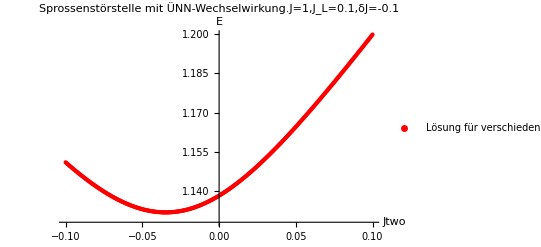

```mathematica
ListPlot[Fueger[moduler[Lister[-1,-0.0005,1.1382837226576603,0.1,0.1]],moduler[Lister[1,0.0005,1.1382837226576603,0.1,0.1]]],AxesLabel->{Jtwo,"E"},PlotLegends->{"Lösung für verschiedene Jtwos"},PlotLabel->"Sprossenstörstelle mit ÜNN-Wechselwirkung.J=1,J_L=0.1,δJ=-0.1",PlotStyle->{Red,PointSize[Small]}]
```

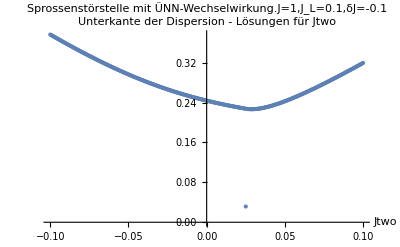

```mathematica
ListPlot[Fueger[differ[-1,0.1,moduler[Lister[-1,-0.0005,1.1382837226576603,0.1,-0.1]]],differ[1,0.1,moduler[Lister[1,0.0005,1.1382837226576603,0.1,-0.1]]]],AxesLabel->{Jtwo,"Unterkante der Dispersion - Lösungen für Jtwo"}, PlotLabel->"Sprossenstörstelle mit ÜNN-Wechselwirkung.J=1,J_L=0.1,δJ=-0.1"]
```

```mathematica
Fueger[moduler[Lister[-1,-0.0005,1.1382837226576603,0.1,0.1]],moduler[Lister[1,0.0005,1.1382837226576603,0.1,0.1]]]
```

{{-0.0005,1.13811},{-0.001,1.13793},{-0.0015,1.13776},{-0.002,1.13759},{-0.0025,1.13742},{-0.003,1.13726},{-0.0035,1.13709},{-0.004,1.13693},{-0.0045,1.13678},{-0.005,1.13662},{-0.0055,1.13647},{-0.006,1.13631},{-0.0065,1.13616},{-0.007,1.13602},{-0.0075,1.13587},{-0.008,1.13573},{-0.0085,1.13559},{-0.009,1.13546},{-0.0095,1.13532},{-0.01,1.13519},{-0.0105,1.13506},{-0.011,1.13493},{-0.0115,1.13481},{-0.012,1.13469},{-0.0125,1.13457},{-0.013,1.13445},{-0.0135,1.13433},{-0.014,1.13422},{-0.0145,1.13411},{-0.015,1.13401},{-0.0155,1.1339},{-0.016,1.1338},{-0.0165,1.1337},{-0.017,1.1336},{-0.0175,1.13351},{-0.018,1.13342},{-0.0185,1.13333},{-0.019,1.13324},{-0.0195,1.13316},{-0.02,1.13308},{-0.0205,1.133},{-0.021,1.13292},{-0.0215,1.13285},{-0.022,1.13278},{-0.0225,1.13271},{-0.023,1.13265},{-0.0235,1.13259},{-0.024,1.13253},{-0.0245,1.13247},{-0.025,1.13242},{-0.0255,1.13236},{-0.026,1.13232},{-0.0265,1.13227},{-0.027,1.13223},{-0.0275,1.13218},{-0.028,1.13215},{-0.0285,1.13211},{-0.029,1.13208},{-0.0295,1.13205},{-0.03,1.13202},{-0.0305,1.132},{-0.031,1.13197},{-0.0315,1.13195},{-0.032,1.13194},{-0.0325,1.13192},{-0.033,1.13191},{-0.0335,1.1319},{-0.034,1.1319},{-0.0345,1.1319},{-0.035,1.1319},{-0.0355,1.1319},{-0.036,1.1319},{-0.0365,1.13191},{-0.037,1.13192},{-0.0375,1.13193},{-0.038,1.13195},{-0.0385,1.13197},{-0.039,1.13199},{-0.0395,1.13201},{-0.04,1.13204},{-0.0405,1.13207},{-0.041,1.1321},{-0.0415,1.13213},{-0.042,1.13217},{-0.0425,1.13221},{-0.043,1.13225},{-0.0435,1.13229},{-0.044,1.13234},{-0.0445,1.13239},{-0.045,1.13244},{-0.0455,1.1325},{-0.046,1.13255},{-0.0465,1.13261},{-0.047,1.13268},{-0.0475,1.13274},{-0.048,1.13281},{-0.0485,1.13288},{-0.049,1.13295},{-0.0495,1.13302},{-0.05,1.1331},{-0.0505,1.13318},{-0.051,1.13326},{-0.0515,1.13335},{-0.052,1.13343},{-0.0525,1.13352},{-0.053,1.13361},{-0.0535,1.13371},{-0.054,1.1338},{-0.0545,1.1339},{-0.055,1.134},{-0.0555,1.13411},{-0.056,1.13421},{-0.0565,1.13432},{-0.057,1.13443},{-0.0575,1.13454},{-0.058,1.13466},{-0.0585,1.13478},{-0.059,1.13489},{-0.0595,1.13502},{-0.06,1.13514},{-0.0605,1.13527},{-0.061,1.13539},{-0.0615,1.13552},{-0.062,1.13566},{-0.0625,1.13579},{-0.063,1.13593},{-0.0635,1.13607},{-0.064,1.13621},{-0.0645,1.13635},{-0.065,1.1365},{-0.0655,1.13664},{-0.066,1.13679},{-0.0665,1.13694},{-0.067,1.1371},{-0.0675,1.13725},{-0.068,1.13741},{-0.0685,1.13757},{-0.069,1.13773},{-0.0695,1.13789},{-0.07,1.13806},{-0.0705,1.13823},{-0.071,1.13839},{-0.0715,1.13857},{-0.072,1.13874},{-0.0725,1.13891},{-0.073,1.13909},{-0.0735,1.13927},{-0.074,1.13945},{-0.0745,1.13963},{-0.075,1.13981},{-0.0755,1.14},{-0.076,1.14019},{-0.0765,1.14038},{-0.077,1.14057},{-0.0775,1.14076},{-0.078,1.14095},{-0.0785,1.14115},{-0.079,1.14135},{-0.0795,1.14155},{-0.08,1.14175},{-0.0805,1.14195},{-0.081,1.14215},{-0.0815,1.14236},{-0.082,1.14257},{-0.0825,1.14278},{-0.083,1.14299},{-0.0835,1.1432},{-0.084,1.14341},{-0.0845,1.14363},{-0.085,1.14385},{-0.0855,1.14406},{-0.086,1.14428},{-0.0865,1.1445},{-0.087,1.14473},{-0.0875,1.14495},{-0.088,1.14518},{-0.0885,1.1454},{-0.089,1.14563},{-0.0895,1.14586},{-0.09,1.14609},{-0.0905,1.14633},{-0.091,1.14656},{-0.0915,1.1468},{-0.092,1.14703},{-0.0925,1.14727},{-0.093,1.14751},{-0.0935,1.14775},{-0.094,1.14799},{-0.0945,1.14824},{-0.095,1.14848},{-0.0955,1.14873},{-0.096,1.14897},{-0.0965,1.14922},{-0.097,1.14947},{-0.0975,1.14972},{-0.098,1.14998},{-0.0985,1.15023},{-0.099,1.15048},{-0.0995,1.15074},{-0.1,1.151},{0.0005,1.13846},{0.001,1.13864},{0.0015,1.13883},{0.002,1.13901},{0.0025,1.1392},{0.003,1.13939},{0.0035,1.13958},{0.004,1.13978},{0.0045,1.13997},{0.005,1.14017},{0.0055,1.14037},{0.006,1.14057},{0.0065,1.14078},{0.007,1.14098},{0.0075,1.14119},{0.008,1.1414},{0.0085,1.14161},{0.009,1.14183},{0.0095,1.14204},{0.01,1.14226},{0.0105,1.14248},{0.011,1.1427},{0.0115,1.14293},{0.012,1.14315},{0.0125,1.14338},{0.013,1.14361},{0.0135,1.14384},{0.014,1.14407},{0.0145,1.14431},{0.015,1.14454},{0.0155,1.14478},{0.016,1.14502},{0.0165,1.14526},{0.017,1.1455},{0.0175,1.14575},{0.018,1.146},{0.0185,1.14624},{0.019,1.14649},{0.0195,1.14674},{0.02,1.147},{0.0205,1.14725},{0.021,1.14751},{0.0215,1.14777},{0.022,1.14802},{0.0225,1.14829},{0.023,1.14855},{0.0235,1.14881},{0.024,1.14908},{0.0245,1.14934},{0.025,1.14961},{0.0255,1.14988},{0.026,1.15015},{0.0265,1.15042},{0.027,1.1507},{0.0275,1.15097},{0.028,1.15125},{0.0285,1.15153},{0.029,1.15181},{0.0295,1.15209},{0.03,1.15237},{0.0305,1.15265},{0.031,1.15294},{0.0315,1.15322},{0.032,1.15351},{0.0325,1.1538},{0.033,1.15409},{0.0335,1.15438},{0.034,1.15467},{0.0345,1.15496},{0.035,1.15526},{0.0355,1.15555},{0.036,1.15585},{0.0365,1.15615},{0.037,1.15644},{0.0375,1.15674},{0.038,1.15704},{0.0385,1.15735},{0.039,1.15765},{0.0395,1.15795},{0.04,1.15826},{0.0405,1.15857},{0.041,1.15887},{0.0415,1.15918},{0.042,1.15949},{0.0425,1.1598},{0.043,1.16011},{0.0435,1.16042},{0.044,1.16074},{0.0445,1.16105},{0.045,1.16137},{0.0455,1.16168},{0.046,1.162},{0.0465,1.16232},{0.047,1.16263},{0.0475,1.16295},{0.048,1.16327},{0.0485,1.1636},{0.049,1.16392},{0.0495,1.16424},{0.05,1.16456},{0.0505,1.16489},{0.051,1.16521},{0.0515,1.16554},{0.052,1.16587},{0.0525,1.16619},{0.053,1.16652},{0.0535,1.16685},{0.054,1.16718},{0.0545,1.16751},{0.055,1.16784},{0.0555,1.16818},{0.056,1.16851},{0.0565,1.16884},{0.057,1.16918},{0.0575,1.16951},{0.058,1.16985},{0.0585,1.17019},{0.059,1.17052},{0.0595,1.17086},{0.06,1.1712},{0.0605,1.17154},{0.061,1.17188},{0.0615,1.17222},{0.062,1.17256},{0.0625,1.1729},{0.063,1.17324},{0.0635,1.17358},{0.064,1.17393},{0.0645,1.17427},{0.065,1.17462},{0.0655,1.17496},{0.066,1.17531},{0.0665,1.17565},{0.067,1.176},{0.0675,1.17635},{0.068,1.17669},{0.0685,1.17704},{0.069,1.17739},{0.0695,1.17774},{0.07,1.17809},{0.0705,1.17844},{0.071,1.17879},{0.0715,1.17914},{0.072,1.17949},{0.0725,1.17985},{0.073,1.1802},{0.0735,1.18055},{0.074,1.18091},{0.0745,1.18126},{0.075,1.18161},{0.0755,1.18197},{0.076,1.18232},{0.0765,1.18268},{0.077,1.18304},{0.0775,1.18339},{0.078,1.18375},{0.0785,1.18411},{0.079,1.18446},{0.0795,1.18482},{0.08,1.18518},{0.0805,1.18554},{0.081,1.1859},{0.0815,1.18626},{0.082,1.18662},{0.0825,1.18698},{0.083,1.18734},{0.0835,1.1877},{0.084,1.18806},{0.0845,1.18843},{0.085,1.18879},{0.0855,1.18915},{0.086,1.18951},{0.0865,1.18988},{0.087,1.19024},{0.0875,1.1906},{0.088,1.19097},{0.0885,1.19133},{0.089,1.1917},{0.0895,1.19206},{0.09,1.19243},{0.0905,1.19279},{0.091,1.19316},{0.0915,1.19352},{0.092,1.19389},{0.0925,1.19426},{0.093,1.19462},{0.0935,1.19499},{0.094,1.19536},{0.0945,1.19573},{0.095,1.1961},{0.0955,1.19646},{0.096,1.19683},{0.0965,1.1972},{0.097,1.19757},{0.0975,1.19794},{0.098,1.19831},{0.0985,1.19868},{0.099,1.19905},{0.0995,1.19942},{0.1,1.19979}}

```mathematica
Fueger[differ[-1,0.1,moduler[Lister[-1,-0.0005,1.1382837226576603,0.1,-0.1]]],differ[1,0.1,moduler[Lister[1,0.0005,1.1382837226576603,0.1,-0.1]]]]
```

{{-0.0005,0.0431185},{-0.001,0.0434008},{-0.0015,0.0436855},{-0.002,0.0439726},{-0.0025,0.0442623},{-0.003,0.0445543},{-0.0035,0.0448489},{-0.004,0.045146},{-0.0045,0.0454456},{-0.005,0.0457477},{-0.0055,0.0460523},{-0.006,0.0463595},{-0.0065,0.0466693},{-0.007,0.0469816},{-0.0075,0.0472966},{-0.008,0.0476141},{-0.0085,0.0479343},{-0.009,0.0482571},{-0.0095,0.0485825},{-0.01,0.0489106},{-0.0105,0.0492413},{-0.011,0.0495748},{-0.0115,0.0499109},{-0.012,0.0502497},{-0.0125,0.0505912},{-0.013,0.0509354},{-0.0135,0.0512824},{-0.014,0.0516321},{-0.0145,0.0519846},{-0.015,0.0523398},{-0.0155,0.0526977},{-0.016,0.0530585},{-0.0165,0.053422},{-0.017,0.0537883},{-0.0175,0.0541575},{-0.018,0.0545294},{-0.0185,0.0549042},{-0.019,0.0552817},{-0.0195,0.0556621},{-0.02,0.0560454},{-0.0205,0.0564315},{-0.021,0.0568204},{-0.0215,0.0572122},{-0.022,0.0576068},{-0.0225,0.0580043},{-0.023,0.0584047},{-0.0235,0.0588079},{-0.024,0.0592141},{-0.0245,0.0596231},{-0.025,0.0600349},{-0.0255,0.0604314},{-0.026,0.0607956},{-0.0265,0.0611294},{-0.027,0.0614347},{-0.0275,0.061713},{-0.028,0.0619661},{-0.0285,0.0621954},{-0.029,0.0624021},{-0.0295,0.0625877},{-0.03,0.0627532},{-0.0305,0.0628997},{-0.031,0.0630284},{-0.0315,0.0631402},{-0.032,0.0632359},{-0.0325,0.0633166},{-0.033,0.0633828},{-0.0335,0.0634355},{-0.034,0.0634753},{-0.0345,0.0635029},{-0.035,0.0635189},{-0.0355,0.0635239},{-0.036,0.0635186},{-0.0365,0.0635034},{-0.037,0.0634788},{-0.0375,0.0634453},{-0.038,0.0634034},{-0.0385,0.0633534},{-0.039,0.0632959},{-0.0395,0.0632311},{-0.04,0.0631595},{-0.0405,0.0630814},{-0.041,0.0629971},{-0.0415,0.062907},{-0.042,0.0628113},{-0.0425,0.0627103},{-0.043,0.0626043},{-0.0435,0.0624936},{-0.044,0.0623783},{-0.0445,0.0622588},{-0.045,0.0621353},{-0.0455,0.0620079},{-0.046,0.0618769},{-0.0465,0.0617425},{-0.047,0.0616048},{-0.0475,0.061464},{-0.048,0.0613203},{-0.0485,0.0611739},{-0.049,0.0610249},{-0.0495,0.0608735},{-0.05,0.0607197},{-0.0505,0.0605638},{-0.051,0.0604059},{-0.0515,0.060246},{-0.052,0.0600844},{-0.0525,0.0599211},{-0.053,0.0597562},{-0.0535,0.0595898},{-0.054,0.059422},{-0.0545,0.059253},{-0.055,0.0590828},{-0.0555,0.0589116},{-0.056,0.0587393},{-0.0565,0.058566},{-0.057,0.0583919},{-0.0575,0.0582171},{-0.058,0.0580415},{-0.0585,0.0578653},{-0.059,0.0576885},{-0.0595,0.0575112},{-0.06,0.0573334},{-0.0605,0.0571552},{-0.061,0.0569767},{-0.0615,0.0567979},{-0.062,0.0566189},{-0.0625,0.0564397},{-0.063,0.0562603},{-0.0635,0.0560808},{-0.064,0.0559013},{-0.0645,0.0557217},{-0.065,0.0555421},{-0.0655,0.0553627},{-0.066,0.0551833},{-0.0665,0.055004},{-0.067,0.0548249},{-0.0675,0.054646},{-0.068,0.0544673},{-0.0685,0.0542888},{-0.069,0.0541107},{-0.0695,0.0539328},{-0.07,0.0537552},{-0.0705,0.0535781},{-0.071,0.0534012},{-0.0715,0.0532248},{-0.072,0.0530488},{-0.0725,0.0528733},{-0.073,0.0526981},{-0.0735,0.0525235},{-0.074,0.0523494},{-0.0745,0.0521757},{-0.075,0.0520026},{-0.0755,0.05183},{-0.076,0.051658},{-0.0765,0.0514866},{-0.077,0.0513157},{-0.0775,0.0511454},{-0.078,0.0509757},{-0.0785,0.0508066},{-0.079,0.0506382},{-0.0795,0.0504704},{-0.08,0.0503032},{-0.0805,0.0501367},{-0.081,0.0499708},{-0.0815,0.0498056},{-0.082,0.0496411},{-0.0825,0.0494772},{-0.083,0.0493141},{-0.0835,0.0491516},{-0.084,0.0489898},{-0.0845,0.0488288},{-0.085,0.0486684},{-0.0855,0.0485088},{-0.086,0.0483499},{-0.0865,0.0481917},{-0.087,0.0480342},{-0.0875,0.0478774},{-0.088,0.0477214},{-0.0885,0.0475661},{-0.089,0.0474115},{-0.0895,0.0472577},{-0.09,0.0471046},{-0.0905,0.0469523},{-0.091,0.0468007},{-0.0915,0.0466498},{-0.092,0.0464997},{-0.0925,0.0463503},{-0.093,0.0462017},{-0.0935,0.0460538},{-0.094,0.0459067},{-0.0945,0.0457603},{-0.095,0.0456146},{-0.0955,0.0454697},{-0.096,0.0453255},{-0.0965,0.0451821},{-0.097,0.0450394},{-0.0975,0.0448975},{-0.098,0.0447563},{-0.0985,0.0446158},{-0.099,0.044476},{-0.0995,0.044337},{-0.1,0.0441988},{0.0005,0.0425611},{0.001,0.042286},{0.0015,0.0420133},{0.002,0.0417429},{0.0025,0.0414749},{0.003,0.0412092},{0.0035,0.0409458},{0.004,0.0406847},{0.0045,0.0404258},{0.005,0.0401693},{0.0055,0.0399149},{0.006,0.0396628},{0.0065,0.0394129},{0.007,0.0391653},{0.0075,0.0389197},{0.008,0.0386764},{0.0085,0.0384352},{0.009,0.0381962},{0.0095,0.0379592},{0.01,0.0377244},{0.0105,0.0374916},{0.011,0.0372609},{0.0115,0.0370323},{0.012,0.0368057},{0.0125,0.0365812},{0.013,0.0363586},{0.0135,0.036138},{0.014,0.0359194},{0.0145,0.0357028},{0.015,0.0354881},{0.0155,0.0352753},{0.016,0.0350644},{0.0165,0.0348554},{0.017,0.0346483},{0.0175,0.0344431},{0.018,0.0342397},{0.0185,0.0340382},{0.019,0.0338384},{0.0195,0.0336405},{0.02,0.0334443},{0.0205,0.0332499},{0.021,0.0330572},{0.0215,0.0328663},{0.022,0.0326771},{0.0225,0.0324896},{0.023,0.0323038},{0.0235,0.0321197},{0.024,0.0319373},{0.0245,0.0317564},{0.025,0.0315772},{0.0255,0.0313997},{0.026,0.0312237},{0.0265,0.0310493},{0.027,0.0308765},{0.0275,0.0307052},{0.028,0.0305355},{0.0285,0.0303673},{0.029,0.0302006},{0.0295,0.0300354},{0.03,0.0298717},{0.0305,0.0297094},{0.031,0.0295487},{0.0315,0.0293893},{0.032,0.0292314},{0.0325,0.0290749},{0.033,0.0289198},{0.0335,0.0287661},{0.034,0.0286137},{0.0345,0.0284627},{0.035,0.0283131},{0.0355,0.0281648},{0.036,0.0280178},{0.0365,0.0278721},{0.037,0.0277278},{0.0375,0.0275847},{0.038,0.0274428},{0.0385,0.0273023},{0.039,0.0271629},{0.0395,0.0270248},{0.04,0.026888},{0.0405,0.0267523},{0.041,0.0266178},{0.0415,0.0264845},{0.042,0.0263524},{0.0425,0.0262215},{0.043,0.0260917},{0.0435,0.025963},{0.044,0.0258355},{0.0445,0.025709},{0.045,0.0255837},{0.0455,0.0254595},{0.046,0.0253363},{0.0465,0.0252142},{0.047,0.0250932},{0.0475,0.0249732},{0.048,0.0248543},{0.0485,0.0247364},{0.049,0.0246195},{0.0495,0.0245036},{0.05,0.0243888},{0.0505,0.0242749},{0.051,0.0241619},{0.0515,0.02405},{0.052,0.023939},{0.0525,0.023829},{0.053,0.0237199},{0.0535,0.0236117},{0.054,0.0235044},{0.0545,0.0233981},{0.055,0.0232926},{0.0555,0.0231881},{0.056,0.0230844},{0.0565,0.0229816},{0.057,0.0228797},{0.0575,0.0227786},{0.058,0.0226784},{0.0585,0.022579},{0.059,0.0224804},{0.0595,0.0223827},{0.06,0.0222857},{0.0605,0.0221896},{0.061,0.0220943},{0.0615,0.0219998},{0.062,0.021906},{0.0625,0.021813},{0.063,0.0217208},{0.0635,0.0216294},{0.064,0.0215387},{0.0645,0.0214487},{0.065,0.0213595},{0.0655,0.021271},{0.066,0.0211832},{0.0665,0.0210962},{0.067,0.0210098},{0.0675,0.0209242},{0.068,0.0208392},{0.0685,0.0207549},{0.069,0.0206713},{0.0695,0.0205884},{0.07,0.0205062},{0.0705,0.0204246},{0.071,0.0203436},{0.0715,0.0202633},{0.072,0.0201837},{0.0725,0.0201046},{0.073,0.0200262},{0.0735,0.0199484},{0.074,0.0198713},{0.0745,0.0197947},{0.075,0.0197188},{0.0755,0.0196434},{0.076,0.0195686},{0.0765,0.0194944},{0.077,0.0194208},{0.0775,0.0193478},{0.078,0.0192753},{0.0785,0.0192034},{0.079,0.0191321},{0.0795,0.0190613},{0.08,0.018991},{0.0805,0.0189213},{0.081,0.0188521},{0.0815,0.0187835},{0.082,0.0187154},{0.0825,0.0186478},{0.083,0.0185807},{0.0835,0.0185141},{0.084,0.018448},{0.0845,0.0183825},{0.085,0.0183174},{0.0855,0.0182528},{0.086,0.0181887},{0.0865,0.0181251},{0.087,0.0180619},{0.0875,0.0179993},{0.088,0.0179371},{0.0885,0.0178753},{0.089,0.017814},{0.0895,0.0177532},{0.09,0.0176928},{0.0905,0.0176329},{0.091,0.0175734},{0.0915,0.0175144},{0.092,0.0174557},{0.0925,0.0173976},{0.093,0.0173398},{0.0935,0.0172824},{0.094,0.0172255},{0.0945,0.017169},{0.095,0.0171129},{0.0955,0.0170572},{0.096,0.0170019},{0.0965,0.016947},{0.097,0.0168925},{0.0975,0.0168384},{0.098,0.0167846},{0.0985,0.0167313},{0.099,0.0166783},{0.0995,0.0166257},{0.1,0.0165735}}

```mathematica
Manipulate[Plot[Sqrt[1+2(Jone*Cos[k]+Jtwo*Cos[2k])],{k,0,Pi},PlotRange->{0.5,2}],{Jone,0,0.1},{Jtwo,-0.1,0.1}]
```